```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Train=Import["NG22P06Problem.xlsx",{"Sheets","Голубович"}][[2;;]];
```

```mathematica
X=Train⟦All,;;2⟧;
```

```mathematica
Y = Train⟦All,3⟧//Round;
```

```mathematica
iCold=Flatten[Position[Y,-1]];
iWarm=Flatten[Position[Y,1]];
```

```mathematica
Fig0=Graphics[
{Blue, Point[X[[iCold]]],Red, Point[X[[iWarm]]]},Frame->True,GridLines->Automatic
];
```

```mathematica
ClearAll[kmIncAS];
kmIncAS[Sigma_,surCharge_,counter_]:=Quiet@Monitor[kmInit[Sigma,surCharge,counter];
While[State!="Stop",Switch[State,
"SVM",ΛS=kmSolveQP[];SVM=kmSVM[kmW0[]];Step++;State="S➫O";
Fig=kmFig[],
"S➫O",State=If[kmDone@"S➫O","SVM","S➫C"],
"S➫C",State=If[kmDone@"S➫C","SVM","O➫S"],
"O➫S",State=If[kmDone@"O➫S","SVM","C➫S"],
"C➫S",State=If[kmDone@"C➫S","SVM","Stop"]]];Fig,Fig];kmFig[];
```

```mathematica
ClearAll[kmInit];
kmInit[Sigma_,surCharge_,counter_]:=(State="SVM";Step=0;σ=Sigma;𝒞=surCharge;Fig=Fig0;
Ker=kmKer[Sigma];
(*Q=ParallelArray[Y⟦iS[[#1]]⟧*Y⟦iS[[#2]]⟧*Ker[X⟦iS[[#1]]⟧,X⟦iS[[#2]]⟧]&,{Length[iS],Length[iS]}];*)
iS=kmSupport[counter];iC={};iO=Complement[Range[Length[X]],iS];
Fig=kmFig[];);
```

```mathematica
ClearAll[kmKer];
kmKer[σ_]:=Compile[{{x,_Real,1},{y,_Real,1}},Exp[-Norm[x-y]^2/(2 σ^2)],Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"];
```

```mathematica
ClearAll[kmSupport];(** ↦iS**)
kmSupport[counter_]:=Block[{step=0,xCold=X⟦iCold⟧,xWarm=X⟦iWarm⟧,iS={},ISC ,ISW},While[step++<counter∧Length@iS<counter,ISC=First[RandomChoice[iCold,1]];ISC = FixedPoint[(ISW=First[Nearest[xWarm->iWarm,X⟦#⟧,1]]; First[Nearest[xCold->iCold,X⟦ISW⟧,1]])&,ISC];AppendTo[iS, {ISC,ISW}]];iS = Flatten@iS;iS = DeleteDuplicates[iS];iS];
```

```mathematica
ClearAll[kmProblemQP];
kmProblemQP[]:=Chop@Flatten@{Qss = ParallelArray[Y⟦iS[[#1]]⟧*Y⟦iS[[#2]]⟧*Ker[X⟦iS[[#1]]⟧,X⟦iS[[#2]]⟧]&,{Length[iS],Length[iS]}];
Qcs = ParallelArray[Y⟦iC[[#1]]⟧*Y⟦iS[[#2]]⟧*Ker[X⟦iC[[#1]]⟧,X⟦iS[[#2]]⟧]&,{Length[iC],Length[iS]}];
Λ =Table[Symbol["λ"<>ToString[i]],{i,Length[iS]}];
ec = Table[1,{i,Length[iC]}];
es = Table[1,{i,Length[iS]}];
spec;If[Qcs=={},spec=0,spec = Qcs.Λ.ec];{(1/2 Qss.#.#+𝒞*spec-es.#),Apply[And, Append[#>=-10&/@Λ,Y[[iS]].#+𝒞*Y[[iC]].ec==0]]}&@Λ};
```

```mathematica
ClearAll[kmSolveQP];(** ↦ΛS**)
kmSolveQP[]:=Block[{tmp=kmProblemQP[]},Values[Last@FindMinimum[tmp,Λ]]]
```

```mathematica
ClearAll[kmW0];
kmW0[]:=Median[Dot[Join[ΛS*Y⟦iS⟧,𝒞* Y⟦iC⟧],Ker[X⟦Flatten[{iS,iC}]⟧,#]]&/@X⟦iS⟧-Y⟦iS⟧];
```

```mathematica
ClearAll[kmSVM];
kmSVM[w0_]:=With[{ΛYsc=Join[ΛS* Y⟦iS⟧,𝒞 *Y⟦iC⟧],Xsc=X⟦Flatten[{iS,iC}]⟧},Compile[{{x,_Real,1}},
ΛYsc.Ker[Xsc,x]-w0,
Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"
]];
```

```mathematica
x1Min=-2;
x1Max = 2;
x2Min = -2;
x2Max = 2;
```

```mathematica
ClearAll[kmFig];
kmFig[]:=Show[Fig0,ContourPlot[SVM@{x1,x2},{x1,x1Min,x1Max},{x2,x2Min,x2Max},Contours->{-1,0,1},ContourStyle->{Blue,Dashed,Red},ContourShading->{{Opacity[0.2],Blue},Opacity[0],Opacity[0],{Opacity[0.2],Red}}
],


Graphics[{AbsoluteThickness[4], Green,Circle[#,Offset[4]]}&/@X⟦iS⟧],
Graphics[{AbsoluteThickness[4], Black,Circle[#,Offset[4]]}&/@X⟦iC⟧],
PlotLabel->StringForm["Step=``,σ=``,C=``,iS=``,iC=``,iO=``",Step,σ,𝒞,Length@iS,Length@iC,Length@iO]];
```

```mathematica
(**Support⟶Outlier**)
ClearAll[kmDone];
kmDone["S➫O"]:=If[Length@iS<2∨0==Length[iBad=Flatten@Position[ΛS,x_ /; x<0,{1}]],(***)False,iBad=RandomChoice[-ΛS[[iBad]]->iBad];
Fig=Show[Fig,Graphics[{AbsoluteThickness[4], Yellow,Circle[X[[iS[[iBad]]]],Offset[4]]}]];
AppendTo[iO,iS[[iBad]]];
iS=Delete[iS,iBad];
(***)True];
```

```mathematica
(**Support⟶Cost**)kmDone["S➫C"]:=If[Length@iS<2∨0==Length[iBad=Flatten@Position[ΛS,x_ /; x>=𝒞,{1}]],(***)False,iBad=RandomChoice[ΛS[[iBad]]->iBad];
Fig=Show[Fig,Graphics[{AbsoluteThickness[4], Yellow,Circle[X[[iS[[iBad]]]],Offset[4]]}]];
AppendTo[iC,iS[[iBad]]];
iS=Delete[iS, iBad];
(***)True];
```

```mathematica
ClearAll[kmMargin];
kmMargin[ind_List]:=Y⟦#⟧*SVM[X⟦#⟧]&/@ind;
kmMargin[ind_]:=Y[[ind]]*SVM[X[[ind]]];
```

```mathematica
(**Outlier⟶Support**)kmDone["O➫S"]:=If[M=kmMargin[iO];
0==Length[iBad=Flatten@Position[M,x_ /; x<=1,{1}]],(***)False,iBad=RandomChoice[Abs@M[[iBad]]->iBad];
Fig=Show[Fig,Graphics[{AbsoluteThickness[4], Yellow,Circle[X[[iO[[iBad]]]],Offset[4]]}]];
AppendTo[iS,iO[[iBad]]];
iO=Delete[iO, iBad];
(***)True];
```

```mathematica
(**Cost⟶Support**)kmDone["C➫S"]:=If[M=kmMargin[iC];
iC=={}∨0==Length[iBad=Flatten@Position[M,x_ /; x>=1,{1}]],(***)False,iBad=RandomChoice[M[[iBad]]->iBad];
Fig=Show[Fig,Graphics[{AbsoluteThickness[4], Yellow,Circle[X[[iC[[iBad]]]],Offset[4]]}]];
AppendTo[iS,iC[[iBad]]];
iC=Delete[iC,iBad];
(***)True];
```

## 8. Обучение SVM - классификатора.

```mathematica
Dynamic@Max[ΛS]
```

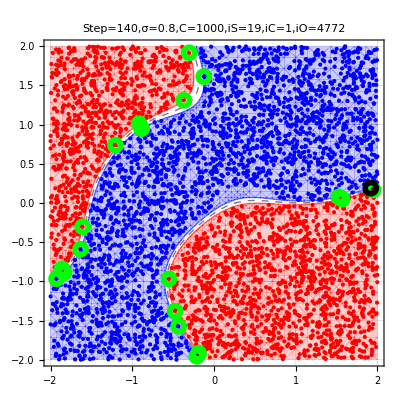

```mathematica
kmIncAS[0.8,1000,20]
```

Лучшие результаты получаются при sigma=1 и при количестве точек около 20